# Perceptrons

Based on this neural network tutorial.

## Classification and Training

```mathematica
Classify[w_,θ_] :=Function[{x},If[ w.x -θ> 0,1,0]]
```

```mathematica
Train:=Function[{inputs,targets,w0,θ0,n},
w=w0;
θ=θ0;
For[i=1,i≤n,i++,
k=Mod[i,4]+1;
in=inputs[[k]];
t=targets[[k]];
o=Classify[w,θ][in];
err=(o-t)0.25;
θ=θ+err;
w=w-in err
];
{w,θ}
];
```

## Evaluation

### Evaluation and visualization functions

```mathematica
Eval:=Function[{inputs,targets,w,θ},
If[Table[Classify[w,θ][x],{x,inputs}]==targets,"Passed","Failed!"]
]
```

```mathematica
PlotSeparator:=Function[{w,θ,vs},
{a,b}=w;
DiskColor:=Function[{i},If[vs[[i]]==1,Green,Red]];
Show[
Plot[(θ-a x)/b,{x,-0.5,1.5},
AspectRatio->1,
Axes->None,
ImageSize->200,
PlotRange->{-0.5,1.5}],
Graphics[
{DiskColor[1],Disk[{1,1},0.1],
DiskColor[2],Disk[{1,0},0.1],
DiskColor[3],Disk[{0,1},0.1],
DiskColor[4],Disk[{0,0},0.1]}
]
]
]
```

### Initial weights and inputs

```mathematica
inputs={{1,1},{1,0},{0,1},{0,0}};
w0=RandomReal[1,2];
θ0=0;
```

### Train and evaluate AND

{{0.271424,0.586856},0.75}

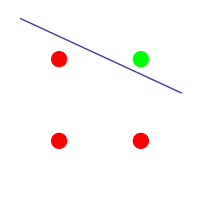

Passed

```mathematica
andTargets={1,0,0,0};
{w,θ}=Train[inputs,andTargets,w0,θ0,50]
PlotSeparator[w,θ,andTargets]
Eval[inputs,andTargets,w,θ]
```

### Train and evaluate OR

{{0.0214244,0.336856},0.}

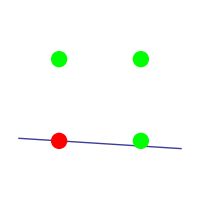

Passed

```mathematica
orTargets={1,1,1,0};
{w,θ}=Train[inputs,orTargets,w0,θ0,50]
PlotSeparator[w,θ,orTargets]
Eval[inputs,orTargets,w,θ]
```

### Train and evaluate XOR

This will fail because XOR is not a linearly separable function!

{{0.0214244,0.336856},0.}

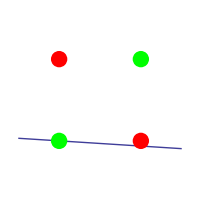

Failed!

```mathematica
xorTargets={1,0,0,1};
{w,θ}=Train[inputs,xorTargets,w0,θ0,100]
PlotSeparator[w,θ,xorTargets]
Eval[inputs,xorTargets,w,θ]
```